```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/Users/meijianli/Documents/Research/ppv2_git/ML/Int

```mathematica
crntdir=NotebookDirectory[]
```

/Users/meijianli/Documents/Research/ppv2_git/ML/

```mathematica
dir=ParentDirectory[ParentDirectory[crntdir]]<>"/Int/"
```

/Users/meijianli/Documents/Research/Int/

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

Note that the I3Fun needs to be multiplied by -i

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

#### I_βs compared with Meijian’s calculation

I_o, same by definition

I_3, mine has an extra -ⅈ factor

I_o+I_1

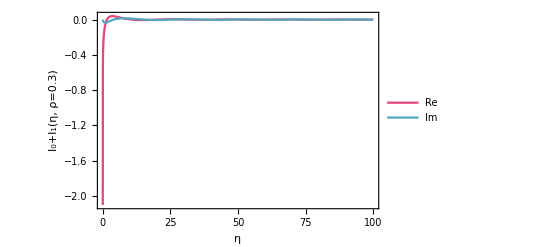

```mathematica
With[{ρ=.3},
Plot[
{Re[I0Fun[ρ,η]+I1Fun[ρ,η]],Im[I0Fun[ρ,η]+I1Fun[ρ,η]]},{η,0,100},
PlotStyle->{color1,color3},
PlotRange->All,
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_0+I_1(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]
]
```

I_1, same, checked numerically

data points generated by Meijian

```mathematica
(* data points generated in my notebook oneGluon_ML *)
listI1etaRe={{0.0001,-2.15381872116264*^-9},{1.0001,-0.03226217236029067},{2.0001,-0.07544932042468327},{3.0001,-0.10326332220033695},{4.0001,-0.10705605082448001},{5.0001,-0.08566886374966284},{6.0001,-0.042469464876974346},{7.0001,0.016286169454196434},{8.0001,0.08266796304208068},{9.0001,0.14811671743789703},{10.0001,0.2043859850473365},{11.0001,0.2443731374575214},{12.0001,0.26280254993331087},{13.0001,0.25671741261622694},{14.0001,0.22574409886730892},{15.0001,0.1721089608906661},{16.0001,0.10040798935835306},{17.0001,0.01715173992781502},{18.0001,-0.0698714721590044},{19.0001,-0.15235418732689607},{20.0001,-0.2222788414246722},{21.0001,-0.2727010067152947},{22.0001,-0.2984328931444739},{23.0001,-0.29656237556233944},{24.0001,-0.2667580908538262},{25.0001,-0.21133107726118688},{26.0001,-0.13504615214511823},{27.0001,-0.04469963041857378},{28.0001,0.05149810275662589},{29.0001,0.14467827328613073},{30.0001,0.2261376292273385},{31.0001,0.28815389884184933},{32.0001,0.3247165591691747},{33.0001,0.3321042050463306},{34.0001,0.3092537359706378},{35.0001,0.2578856357160048},{36.0001,0.18237206026828168},{37.0001,0.08935821080059886},{38.0001,-0.012829639084842193},{39.0001,-0.11493618335862982},{40.0001,-0.20762083184499447},{41.0001,-0.2823159625369884},{42.0001,-0.3320207007806845},{43.0001,-0.35195673737435307},{44.0001,-0.34002497237514},{45.0001,-0.2970197307403638},{46.0001,-0.2265793138234828},{47.0001,-0.1348757236225754},{48.0001,-0.030070325834228695},{49.0001,0.0784161899636075},{50.0001,0.18075392625018233},{51.0001,0.2675969967394341},{52.0001,0.3309385147269944},{53.0001,0.3648490684086425},{54.0001,0.3660306183861611},{55.0001,0.33413423283526045},{56.0001,0.27181134129402484},{57.0001,0.18449231910043432},{58.0001,0.0799110230716741},{59.0001,-0.032582872948001176},{60.0001,-0.1428623690301812},{61.0001,-0.2409370541905225},{62.0001,-0.31785981021761367},{63.0001,-0.3665439181583608},{64.0001,-0.3824159206384078},{65.0001,-0.3638441498733165},{66.0001,-0.3123029103098091},{67.0001,-0.23225610483569167},{68.0001,-0.1307694683196456},{69.0001,-0.016885224920974093},{70.0001,0.09918532368654388},{71.0001,0.20697902252545458},{72.0001,0.29672537321615877},{73.0001,0.36023296829776713},{74.0001,0.3916373753092911},{75.0001,0.3879421905000132},{76.0001,0.34930340769610096},{77.0001,0.2790302596305753},{78.0001,0.1833012208764702},{79.0001,0.07061961200133239},{80.0001,-0.0489431154663879},{81.0001,-0.16464895037078703},{82.0001,-0.2660589284420098},{83.0001,-0.3439758491284819},{84.0001,-0.3912789061821875},{85.0001,-0.403574467154994},{86.0001,-0.3796035467679596},{87.0001,-0.3213682573537139},{88.0001,-0.23396474138425918},{89.0001,-0.12513653062363972},{90.0001,-0.00458755055202931},{91.0001,0.11688418811240676},{92.0001,0.22835477789607123},{93.0001,0.3197575882501813},{94.0001,0.38279287320902106},{95.0001,0.41168158556619766},{96.0001,0.4036949292348257},{97.0001,0.3594111587220198},{98.0001,0.2826755482723322},{99.0001,0.18026611599341405}};
listI1etaIm={{0.0001,-4.33889303714494*^-14},{1.0001,-0.0068634011500828245},{2.0001,-0.03442204139161652},{3.0001,-0.07922011141269432},{4.0001,-0.13178998192958763},{5.0001,-0.18186744644670652},{6.0001,-0.2204138734202472},{7.0001,-0.2406140635164422},{8.0001,-0.2383856062239735},{9.0001,-0.21256740507681565},{10.0001,-0.1648432866010821},{11.0001,-0.09942821844567044},{12.0001,-0.022547477961680856},{13.0001,0.05824742762003146},{14.0001,0.13486772676322722},{15.0001,0.19951203407973972},{16.0001,0.24545280800398148},{17.0001,0.2677131421433331},{18.0001,0.2635718252151983},{19.0001,0.23285009953709088},{20.0001,0.17795362237325432},{21.0001,0.10366584671788767},{22.0001,0.016712210913823015},{23.0001,-0.07486402429373962},{24.0001,-0.16245577594825336},{25.0001,-0.2377051882263372},{26.0001,-0.2932992613776458},{27.0001,-0.32367300797951243},{28.0001,-0.32555351110830244},{29.0001,-0.2982928971207704},{30.0001,-0.24395775449290255},{31.0001,-0.1671651215910165},{32.0001,-0.07467874486242171},{33.0001,0.02519830694151688},{34.0001,0.12337947202184946},{35.0001,0.21082969891815753},{36.0001,0.2794026466461601},{37.0001,0.32260248821486237},{38.0001,0.3361992795703713},{39.0001,0.31864000194627734},{40.0001,0.2712159329878933},{41.0001,0.19796926161803186},{42.0001,0.10534575222036384},{43.0001,0.0016240476995354287},{44.0001,-0.10382833709333722},{45.0001,-0.20140356110271868},{46.0001,-0.2821307567266967},{47.0001,-0.3385018000630881},{48.0001,-0.3651676189365907},{49.0001,-0.35944360173138445},{50.0001,-0.3215734073258621},{51.0001,-0.25472903417631},{52.0001,-0.16474199853451338},{53.0001,-0.05959108546124467},{54.0001,0.05130905466253011},{55.0001,0.15795459289868308},{56.0001,0.25065811687432865},{57.0001,0.32093099043892404},{58.0001,0.36226202539553665},{59.0001,0.37072108634965345},{60.0001,0.34533151375193993},{61.0001,0.28817690640269955},{62.0001,0.2042302893271848},{63.0001,0.10092035669639424},{64.0001,-0.012527455640778139},{65.0001,-0.125916384145464},{66.0001,-0.22899620439870433},{67.0001,-0.3123907788902177},{68.0001,-0.36845125049696126},{69.0001,-0.3919572021675098},{70.0001,-0.38060153190395096},{71.0001,-0.33521410324967627},{72.0001,-0.2597026970088908},{73.0001,-0.16071529874277782},{74.0001,-0.047053004802066416},{75.0001,0.07111447123756764},{76.0001,0.18316062552907836},{77.0001,0.2789594434408866},{78.0001,0.34980179873052697},{79.0001,0.38918798042131836},{80.0001,0.39342421545644696},{81.0001,0.36196847945094607},{82.0001,0.2974931738772613},{83.0001,0.20565875112734175},{84.0001,0.09461528330472475},{85.0001,-0.02572106974401548},{86.0001,-0.14455459609512802},{87.0001,-0.25117945972219635},{88.0001,-0.33594454366503},{89.0001,-0.39112739589575063},{90.0001,-0.41163754086553095},{91.0001,-0.39548535452048605},{92.0001,-0.3439733213426854},{93.0001,-0.26159141756653453},{94.0001,-0.15562497683800733},{95.0001,-0.03550934256636104},{96.0001,0.08801144754895059},{97.0001,0.20384684336850212},{98.0001,0.30155658452861106},{99.0001,0.3722924696026915}};
```

plot

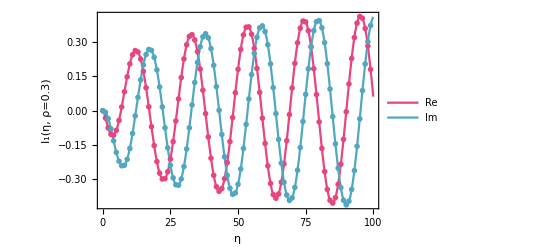

```mathematica
With[{ρ=.3},
Show[
Plot[
{Re[I1Fun[ρ,η]],Im[I1Fun[ρ,η]]},{η,0,100},
PlotStyle->{color1,color3},
PlotRange->All,
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_1(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
],
ListPlot[{listI1etaRe,listI1etaIm},
PlotTheme->"OpenMarkers",
PlotStyle->{color1,color3}]
]
]
```

I_2, mine has an extra -ⅈ factor, checked numerically

data points generated by Meijian

```mathematica
(* data points generated in my notebook oneGluon_ML *)
listI2etaRe={{0.0001,1.32825546405078*^-6},{1.0001,0.01418594737442219},{2.0001,0.030949912074070565},{3.0001,0.049720164297212995},{4.0001,0.06905116093200388},{5.0001,0.08732762671186163},{6.0001,0.10306260113578913},{7.0001,0.11505466567516227},{8.0001,0.12247319837132967},{9.0001,0.12489676237314863},{10.0001,0.12231540482418223},{11.0001,0.11510286380326064},{12.0001,0.10396353722253937},{13.0001,0.08985938400280903},{14.0001,0.07392268258688696},{15.0001,0.05736125540362061},{16.0001,0.04136311462818706},{17.0001,0.027007369534544003},{18.0001,0.015187626312403776},{19.0001,0.006553041152380381},{20.0001,0.001470739409201487},{21.0001,0.000011605197876939262},{22.0001,0.0019596156865407323},{23.0001,0.006843089679685923},{24.0001,0.013984583447862244},{25.0001,0.022564824649484318},{26.0001,0.03169512802115031},{27.0001,0.04049225101242332},{28.0001,0.0481496520259036},{29.0001,0.05399959676426745},{30.0001,0.057561469526272974},{31.0001,0.058572902827967614},{32.0001,0.057001831099266875},{33.0001,0.053039278041866825},{34.0001,0.047073453948210824},{35.0001,0.03965001555416879},{36.0001,0.03141881703759379},{37.0001,0.02307541371426347},{38.0001,0.015300297346043708},{39.0001,0.008701666262374466},{40.0001,0.0037662800704567944},{41.0001,0.0008222385643564378},{42.0001,0.000016417515005348604},{43.0001,0.0013079909904689005},{44.0001,0.004478083652605184},{45.0001,0.009154244312177756},{46.0001,0.014847261336152356},{47.0001,0.020996590649166202},{48.0001,0.027021021866666953},{49.0001,0.0323689224505868},{50.0001,0.03656499855804008},{51.0001,0.039248965297039015},{52.0001,0.04020329130607063},{53.0001,0.039367909059541906},{54.0001,0.03684098116522432},{55.0001,0.03286602468079721},{56.0001,0.027806852160157103},{57.0001,0.022112792927429237},{58.0001,0.01627742910304754},{59.0001,0.01079455788175974},{60.0001,0.006115240440795549},{61.0001,0.0026096131947857485},{62.0001,0.0005366419635070615},{63.0001,0.000024243000101478035},{64.0001,0.0010612470494251562},{65.0001,0.0035016415013840677},{66.0001,0.007080370087508878},{67.0001,0.011439245790287395},{68.0001,0.016160264070082003},{69.0001,0.020803446744265187},{70.0001,0.024945760918186604},{71.0001,0.028217722184923875},{72.0001,0.030334549962348568},{73.0001,0.03111926629774806},{74.0001,0.03051597109081582},{75.0001,0.028592148270193643},{76.0001,0.02553027368877913},{77.0001,0.021609480349126783},{78.0001,0.017179150395663104},{79.0001,0.012626881255327946},{80.0001,0.0083437292726398},{81.0001,0.004689816735796189},{82.0001,0.001963299188446576},{83.0001,0.0003753419238240012},{84.0001,0.00003318234281411356},{85.0001,0.0009326120453842443},{86.0001,0.0029603666223225796},{87.0001,0.00590603743861564},{88.0001,0.00948229472337823},{89.0001,0.013351505981524233},{90.0001,0.01715630753215992},{91.0001,0.020551382733203914},{92.0001,0.023233641046459308},{93.0001,0.024968178734058235},{94.0001,0.02560781441661141},{95.0001,0.02510459137626017},{96.0001,0.0235123681554719},{97.0001,0.020980413918333517},{98.0001,0.01773871475680339},{99.0001,0.014076412716193747}};
listI2etaIm={{0.0001,-0.08880300879024035},{1.0001,-0.09385308483997884},{2.0001,-0.10004733459616803},{3.0001,-0.10292462075591435},{4.0001,-0.10092855197983922},{5.0001,-0.09373693748562073},{6.0001,-0.08178292600788103},{7.0001,-0.06599532880712111},{8.0001,-0.047612962559770364},{9.0001,-0.028031824675416518},{10.0001,-0.008672133933100784},{11.0001,0.009137418409732414},{12.0001,0.024256705070635372},{13.0001,0.03580959638421564},{14.0001,0.04323500688726785},{15.0001,0.0463117526745514},{16.0001,0.04515689415108008},{17.0001,0.04019893049223236},{18.0001,0.03212889411348607},{19.0001,0.021833882434350638},{20.0001,0.010318716279997867},{21.0001,-0.001377872970542194},{22.0001,-0.012265910241648793},{23.0001,-0.021479376201928864},{24.0001,-0.028338394481980344},{25.0001,-0.03239404982351987},{26.0001,-0.03345297781458841},{27.0001,-0.0315805488722158},{28.0001,-0.027083198085697542},{29.0001,-0.020472089774680985},{30.0001,-0.012411722666965243},{31.0001,-0.003658170376634528},{32.0001,0.005007666957562048},{33.0001,0.012846195116327001},{34.0001,0.01921926805758399},{35.0001,0.023639625288328865},{36.0001,0.025805933810703126},{37.0001,0.025621040135198912},{38.0001,0.02319249297372465},{39.0001,0.018815888228282982},{40.0001,0.012942991479213694},{41.0001,0.006137796092960848},{42.0001,-0.0009754167902412923},{43.0001,-0.0077674043556339445},{44.0001,-0.013657914919142786},{45.0001,-0.01816376134102948},{46.0001,-0.02093713175722543},{47.0001,-0.021791185536716898},{48.0001,-0.02071113653564573},{49.0001,-0.017850300752826453},{50.0001,-0.013511871519962821},{51.0001,-0.008118374072948638},{52.0001,-0.0021717450442895747},{53.0001,0.0037922980334912024},{54.0001,0.009251541003020787},{55.0001,0.013742117629699905},{56.0001,0.0168971324088065},{57.0001,0.018475905484282823},{58.0001,0.018381563479790055},{59.0001,0.016665753539157783},{60.0001,0.013520391366724095},{61.0001,0.009257469174540735},{62.0001,0.0042789514342475195},{63.0001,-0.0009604079466961554},{64.0001,-0.00599394864433642},{65.0001,-0.010384066046819459},{66.0001,-0.013759705201695126},{67.0001,-0.015847216672411277},{68.0001,-0.016492046707167703},{69.0001,-0.015669580771028147},{70.0001,-0.013484433535584282},{71.0001,-0.010158493474068966},{72.0001,-0.006008998024134807},{73.0001,-0.001418753349081061},{74.0001,0.003198748731470696},{75.0001,0.007436176350275176},{76.0001,0.010927917270706224},{77.0001,0.013381279609163759},{78.0001,0.014600699169979053},{79.0001,0.014502977870677407},{80.0001,0.013122395851846257},{81.0001,0.010605443394909372},{82.0001,0.007195827824311274},{83.0001,0.003211246173011337},{84.0001,-0.000985894705616129},{85.0001,-0.005021140174607992},{86.0001,-0.00854111402732408},{87.0001,-0.011244201884569005},{88.0001,-0.012906148954929059},{89.0001,-0.013398419453841987},{90.0001,-0.012697834589945067},{91.0001,-0.010886793841241563},{92.0001,-0.00814421966765166},{93.0001,-0.004728175234344292},{94.0001,-0.0009518179754875022},{95.0001,0.0028450917859127317},{96.0001,0.006326554510913376},{97.0001,0.009189871951315449},{98.0001,0.011191783991601334},{99.0001,0.012168960345244954}};
```

plot

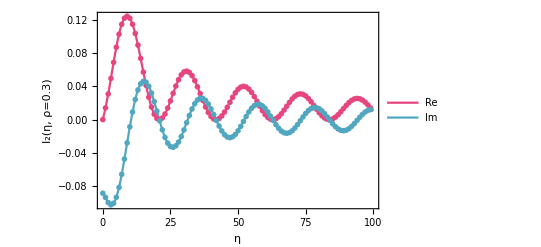

```mathematica
With[{ρ=.3},
Show[
Plot[
{Im[I2Fun[ρ,η]],-Re[I2Fun[ρ,η]]},{η,0,100},
PlotStyle->{color1,color3},
PlotRange->All,
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_2(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
],
ListPlot[{listI2etaRe,listI2etaIm},
PlotTheme->"OpenMarkers",
PlotStyle->{color1,color3}]
]
]
```

#### J2

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

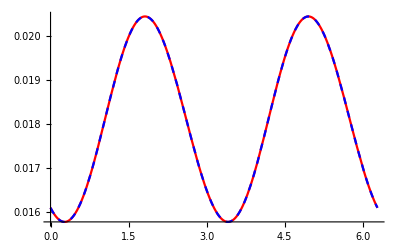

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

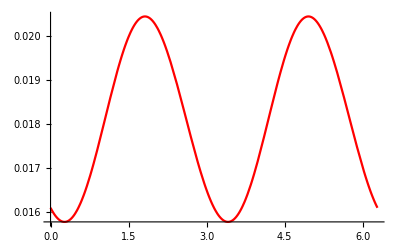

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

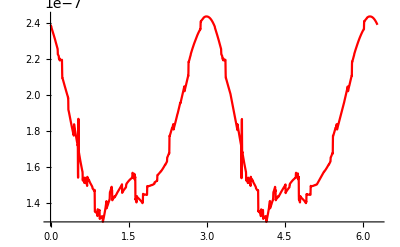

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

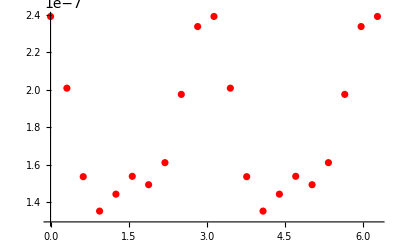

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
Print["v_2=",NIntegrate[dσ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
FNv2[f_Function]:=
NIntegrate[dσ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]
```

### b = 0, kT = 1.0

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

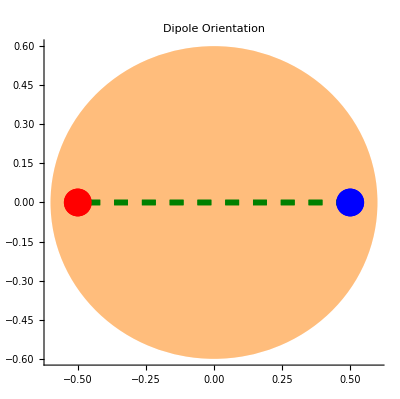

NIntegrate::inumr: The integrand (Cos[2 ϕ$1206970] J2CompileN[1. Cos[ϕ$1206970],1. Sin[ϕ$1206970],0,0,500000000000001/1000000000000000,0,-499999999999999/1000000000000000,0,1/2,0,«2»])/(1. Cos[ϕ$1206970]^2+1. Sin[ϕ$1206970]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::inumr: The integrand (J2CompileN[1. Cos[ϕ$1206970],1. Sin[ϕ$1206970],0,0,500000000000001/1000000000000000,0,-499999999999999/1000000000000000,0,1/2,0,«2»] Sin[2 ϕ$1206970])/(1. Cos[ϕ$1206970]^2+1. Sin[ϕ$1206970]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::inumr: The integrand (Cos[2 ϕ$1206970] J2CompileN[1. Cos[ϕ$1206970],1. Sin[ϕ$1206970],0,0,500000000000001/1000000000000000,0,-499999999999999/1000000000000000,0,1/2,0,«2»])/(1. Cos[ϕ$1206970]^2+1. Sin[ϕ$1206970]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{NIntegrate[(Cos[2 ϕ$1206970] J2CompileN[1. Cos[ϕ$1206970],1. Sin[ϕ$1206970],0,0,500000000000001/1000000000000000,0,-499999999999999/1000000000000000,0,1/2,0,-1/2,0])/(1. Cos[ϕ$1206970]^2+1. Sin[ϕ$1206970]^2),{ϕ$1206970,0,2 π}]/NIntegrate[dσHZ[{1/2,0},x2u$1206970,{1/1000000000000000,0}+{1/2,0},{1/1000000000000000,0}+x4u$1206970,{1.,ϕ$1206970}],{ϕ$1206970,0,2 π}],NIntegrate[(J2CompileN[1. Cos[ϕ$1206970],1. Sin[ϕ$1206970],0,0,500000000000001/1000000000000000,0,-499999999999999/1000000000000000,0,1/2,0,-1/2,0] Sin[2 ϕ$1206970])/(1. Cos[ϕ$1206970]^2+1. Sin[ϕ$1206970]^2),{ϕ$1206970,0,2 π}]/NIntegrate[dσHZ[{1/2,0},x2u$1206970,{1/1000000000000000,0}+{1/2,0},{1/1000000000000000,0}+x4u$1206970,{1.,ϕ$1206970}],{ϕ$1206970,0,2 π}]}

```mathematica
x1u={1/2,0};
x3u={1/2,0};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

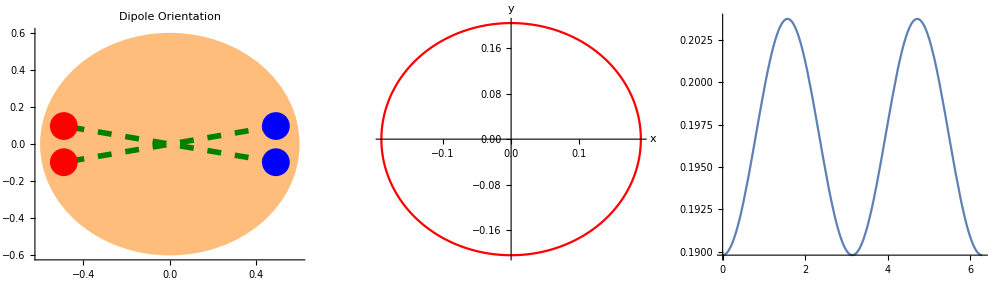

{-0.0177289,2.82249×10^-8}

{-0.0177289,2.82249×10^-8}

```mathematica
θ=π/16;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
showdσHZ[bu,x1u,x3u,kT,False]
```

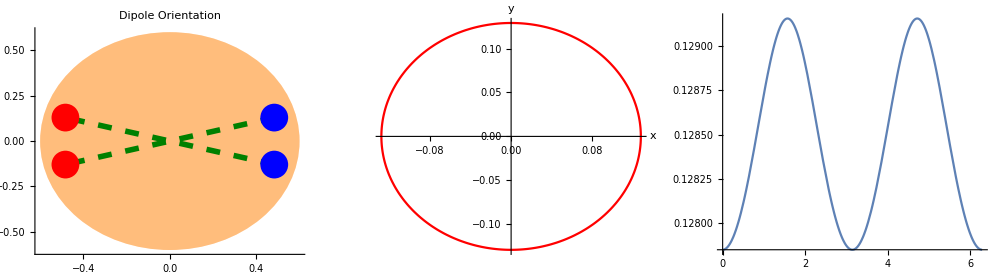

{-0.00254539,3.60683×10^-8}

```mathematica
θ=π/12;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

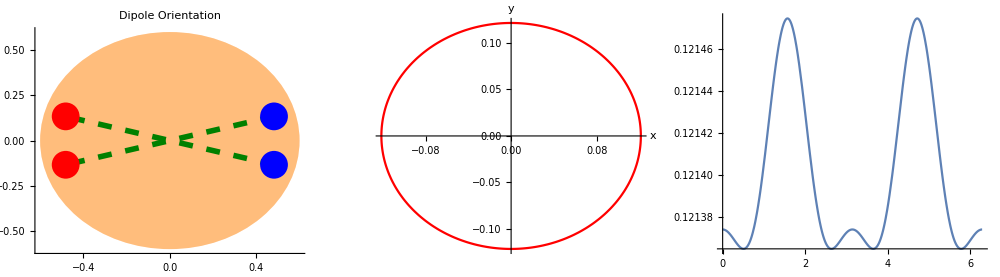

{-0.000204641,6.48675×10^-8}

```mathematica
θ=π/11.6;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

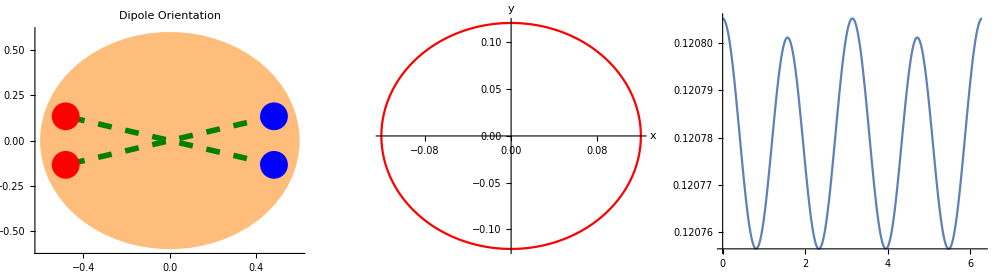

{0.0000110804,6.6607×10^-8}

```mathematica
θ=π/11.565;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

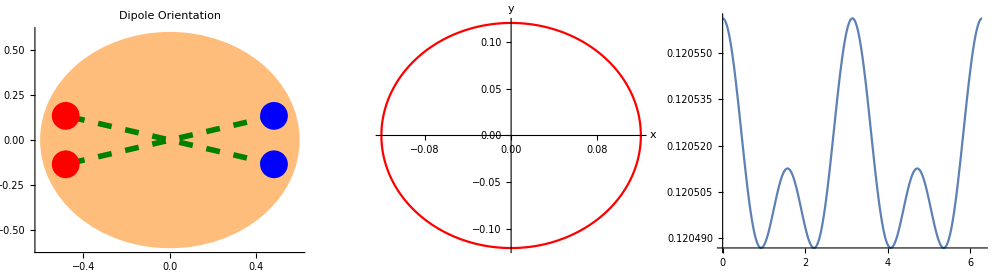

{0.000104099,6.73066×10^-8}

```mathematica
θ=π/11.55;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

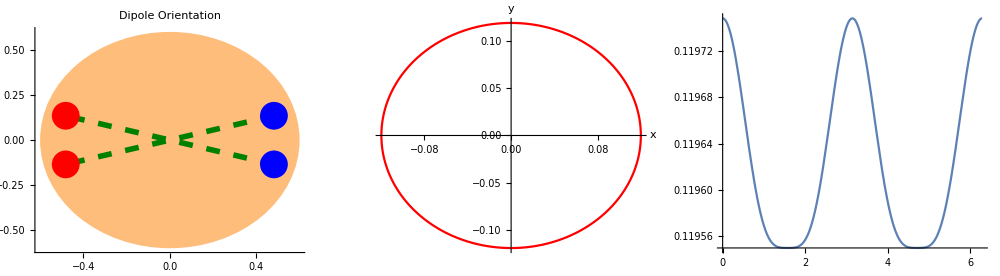

{0.000416641,6.94326×10^-8}

```mathematica
θ=π/11.5;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

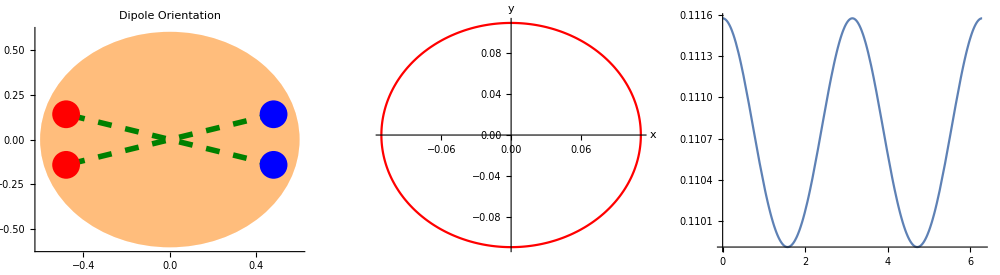

{0.0037672,7.01327×10^-8}

```mathematica
θ=π/11;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

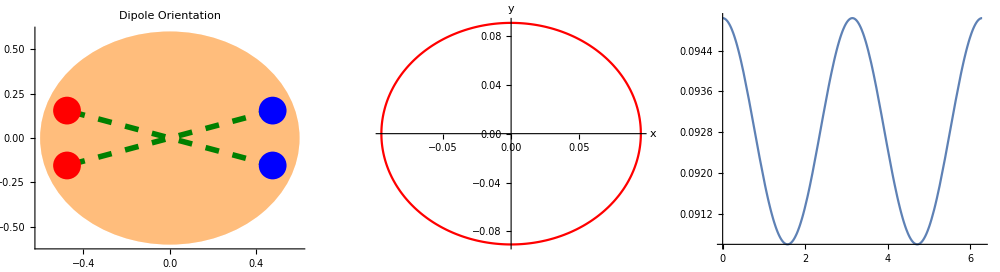

{0.0119718,4.14811×10^-8}

```mathematica
θ=π/10;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

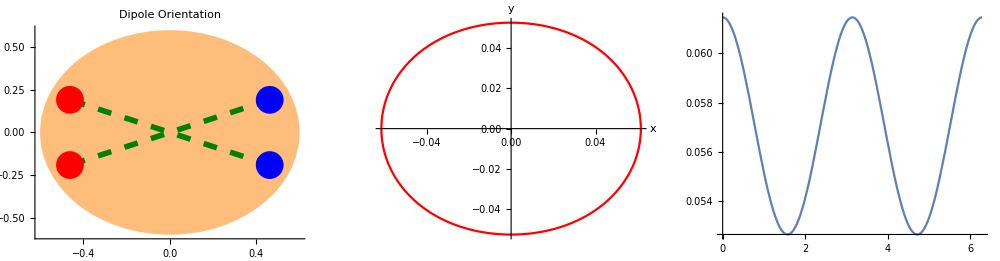

{0.0385892,5.356×10^-8}

```mathematica
θ=π/8;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

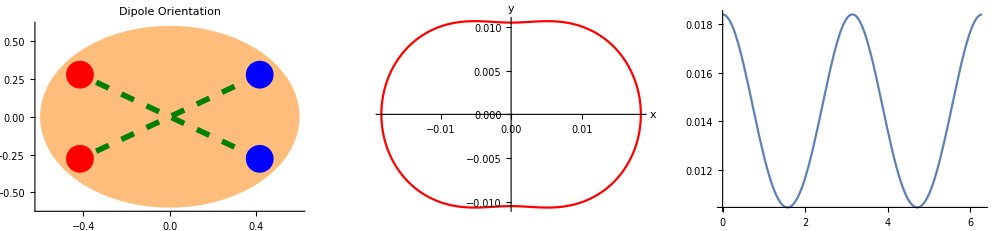

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$6856288 near {ϕ$6856288} = {6.0340560481230842426736415973209659568965435028076171875}. NIntegrate obtained -2.37721×10^-9 and 2.92058×10^-13 for the integral and error estimates.

{0.138345,-2.64589×10^-8}

```mathematica
θ=(3π)/16;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

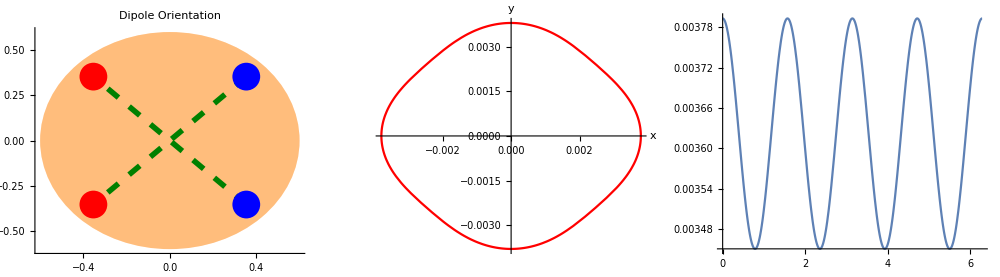

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7038328 near {ϕ$7038328} = {4.71229}. NIntegrate obtained -9.21572×10^-19 and 2.0574×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7038328 near {ϕ$7038328} = {2.95742}. NIntegrate obtained -1.42275×10^-9 and 1.50031×10^-13 for the integral and error estimates.

{-4.04974×10^-17,-6.25213×10^-8}

```mathematica
θ=π/4;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

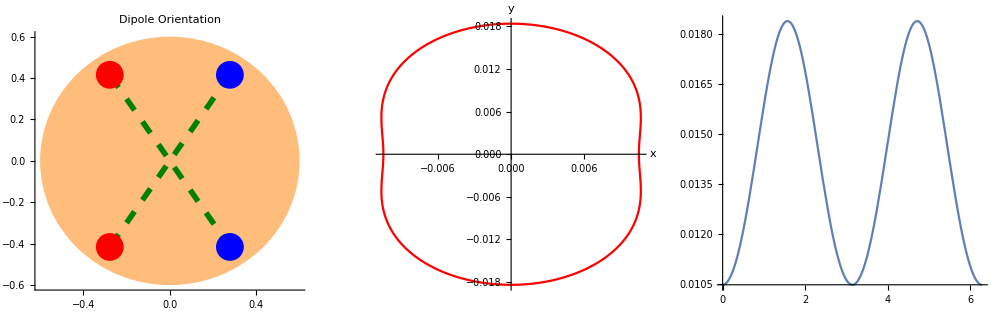

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7318653 near {ϕ$7318653} = {3.30103}. NIntegrate obtained -2.35215×10^-9 and 2.24338×10^-13 for the integral and error estimates.

{-0.138345,-2.618×10^-8}

```mathematica
θ=(5π)/16;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

```mathematica
v2b0=Table[{2 ϕ/π,
showdσHZ[{10^-15,0},1/2{Cos[ϕ],Sin[ϕ]},1/2{Cos[-ϕ],Sin[-ϕ]},1.0,False][[1]]},{ϕ,0,π/2,π/(2*100)}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10544523 near {ϕ$10544523} = {1.70569}. NIntegrate obtained -1.33227×10^-15 and 2.94376×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10601491 near {ϕ$10601491} = {4.58957}. NIntegrate obtained -1.71568×10^-11 and 4.36288×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10658447 near {ϕ$10658447} = {1.44798}. NIntegrate obtained -8.84074×10^-11 and 4.46552×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0,-0.0633491},{1/200,-0.050048},{1/100,-0.0467814},{3/200,-0.0440411},{1/50,-0.0414763},{1/40,-0.0389593},{3/100,-0.0364261},{7/200,-0.0338381},{1/25,-0.0311695},{9/200,-0.0284013},{1/20,-0.0255183},{11/200,-0.0225077},{3/50,-0.0193586},{13/200,-0.0160608},{7/100,-0.0126048},{3/40,-0.00898139},{2/25,-0.00518134},{17/200,-0.00119559},{9/100,0.00298531},{19/200,0.0073711},{1/10,0.0119718},{21/200,0.0167979},{11/100,0.0218608},{23/200,0.027172},{3/25,0.0327438},{1/8,0.0385892},{13/100,0.0447217},{27/200,0.0511549},{7/50,0.0579025},{29/200,0.064978},{3/20,0.0723931},{31/200,0.0801574},{4/25,0.0882761},{33/200,0.096747},{17/100,0.105557},{7/40,0.114675},{9/50,0.124045},{37/200,0.13357},{19/100,0.143095},{39/200,0.152382},{1/5,0.161067},{41/200,0.168617},{21/100,0.174264},{43/200,0.176945},{11/50,0.175259},{9/40,0.167494},{23/100,0.151823},{47/200,0.126747},{6/25,0.0918165},{49/200,0.0484009},{1/4,-4.04974×10^-17},{51/200,-0.0484009},{13/50,-0.0918165},{53/200,-0.126747},{27/100,-0.151823},{11/40,-0.167494},{7/25,-0.175259},{57/200,-0.176945},{29/100,-0.174264},{59/200,-0.168617},{3/10,-0.161067},{61/200,-0.152382},{31/100,-0.143095},{63/200,-0.13357},{8/25,-0.124045},{13/40,-0.114675},{33/100,-0.105557},{67/200,-0.096747},{17/50,-0.0882761},{69/200,-0.0801574},{7/20,-0.0723931},{71/200,-0.064978},{9/25,-0.0579025},{73/200,-0.0511549},{37/100,-0.0447217},{3/8,-0.0385892},{19/50,-0.0327438},{77/200,-0.027172},{39/100,-0.0218608},{79/200,-0.0167979},{2/5,-0.0119718},{81/200,-0.0073711},{41/100,-0.00298531},{83/200,0.0011956},{21/50,0.00518134},{17/40,0.00898139},{43/100,0.0126048},{87/200,0.0160608},{11/25,0.0193586},{89/200,0.0225077},{9/20,0.0255183},{91/200,0.0284013},{23/50,0.0311695},{93/200,0.0338381},{47/100,0.0364261},{19/40,0.0389593},{12/25,0.0414763},{97/200,0.0440411},{49/100,0.0467814},{99/200,0.050048},{1/2,0.063349}}

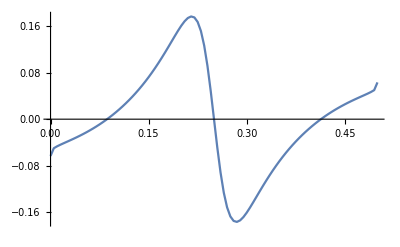

```mathematica
ListPlot[v2b0,Joined->True]
```

### b != 0

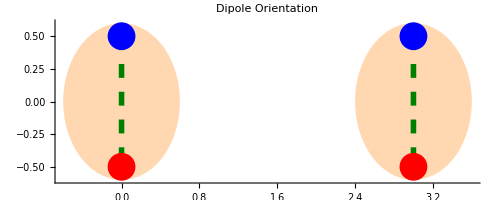

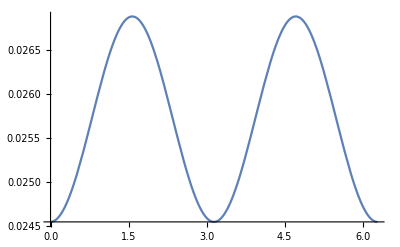

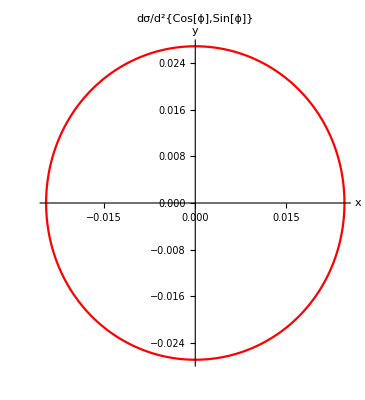

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$882143 near {ϕ$882143} = {0.0000241858}. NIntegrate obtained -3.76218×10^-16+0. ⅈ and 1.90296×10^-16 for the integral and error estimates.

v_2={-0.0226608+0. ⅈ,-2.32945×10^-15+0. ⅈ}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

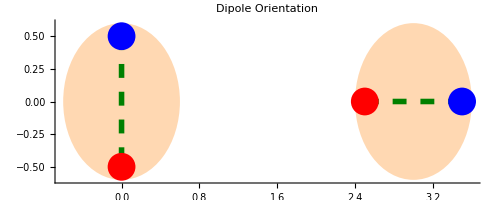

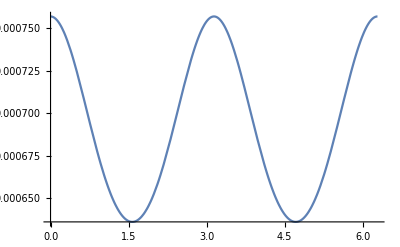

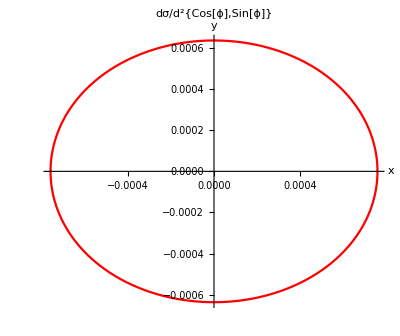

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2364862 near {ϕ$2364862} = {4.00052}. NIntegrate obtained -3.48842×10^-17+1.00965×10^-21 ⅈ and 2.01245×10^-17 for the integral and error estimates.

v_2={0.043477,-8.00443×10^-15+2.3167×10^-19 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

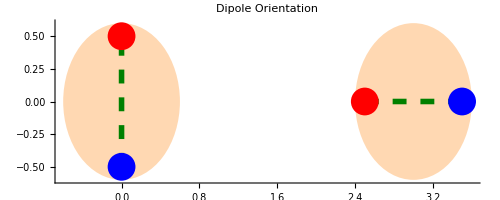

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2714314 near {ϕ$2714314} = {4.00052}. NIntegrate obtained -3.48842×10^-17+1.00965×10^-21 ⅈ and 2.01245×10^-17 for the integral and error estimates.

v_2={0.043477,-8.00443×10^-15+2.3167×10^-19 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

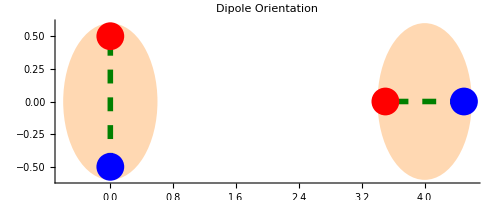

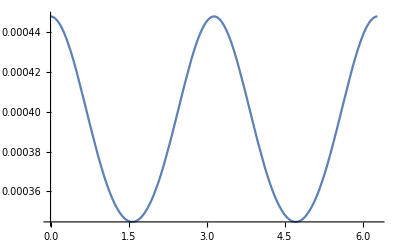

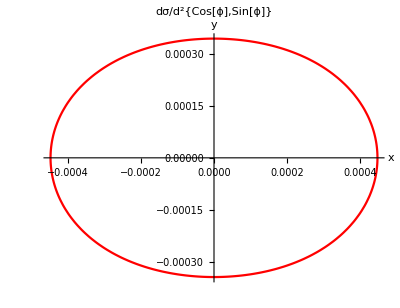

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3063766 near {ϕ$3063766} = {4.02507}. NIntegrate obtained -1.00119×10^-17-1.40336×10^-21 ⅈ and 9.16594×10^-18 for the integral and error estimates.

v_2={0.0654057,-4.05025×10^-15-5.67719×10^-19 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={4,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

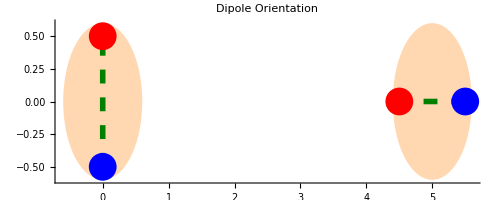

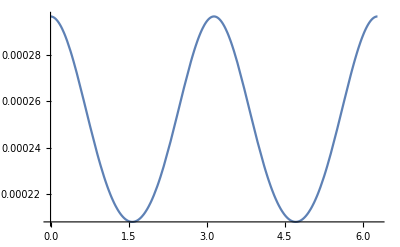

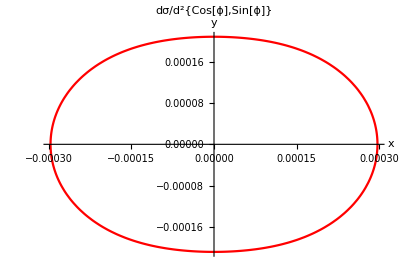

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3419232 near {ϕ$3419232} = {3.68146}. NIntegrate obtained 1.29596×10^-18+2.28256×10^-22 ⅈ and 6.74086×10^-18 for the integral and error estimates.

v_2={0.0888849,8.26034×10^-16+1.45489×10^-19 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={5,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

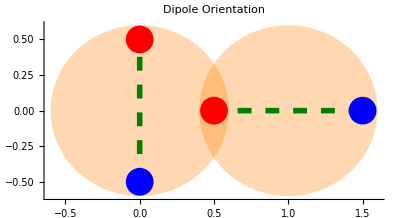

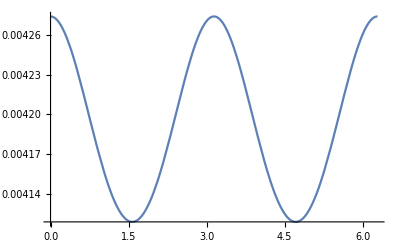

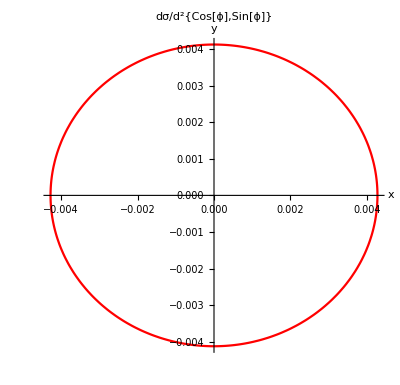

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3768926 near {ϕ$3768926} = {0.797572}. NIntegrate obtained 8.21121×10^-16+3.2285×10^-21 ⅈ and 4.51298×10^-16 for the integral and error estimates.

v_2={0.00924929,3.11594×10^-14+1.22513×10^-19 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

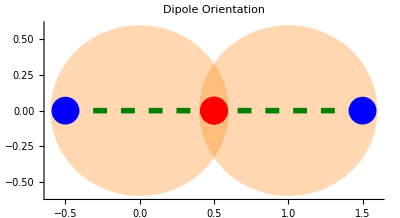

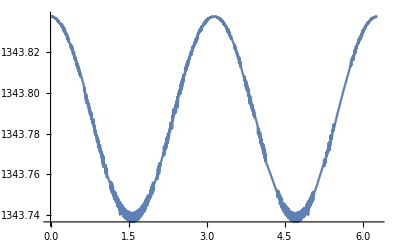

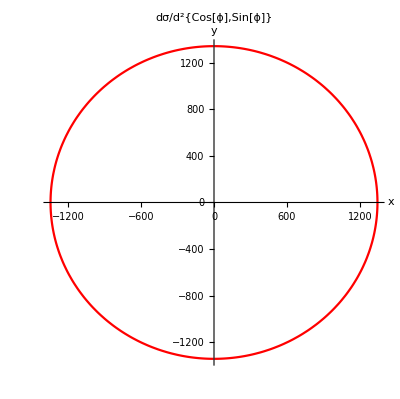

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$4132843 near {ϕ$4132843} = {4.56508}. NIntegrate obtained 0.156532+0. ⅈ and 0.000518402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$4132843 near {ϕ$4132843} = {2.34387}. NIntegrate obtained -0.000203444+0. ⅈ and 0.000262033 for the integral and error estimates.

v_2={0.0000185393,-2.40954×10^-8+0. ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{1+10^-10,0};
bu={1,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```